```mathematica
(* https://en.wikipedia.org/wiki/Entropic_uncertainty*)
```

```mathematica
(* Ha+Hb=Log[e/2]:Log[Det[guv]]+Log[Det[gbaruv]=Log[e/2]*)
```

```mathematica
(* As guv Poincare disk:gbarvu as half plane*)
```

```mathematica
Reduce[x*(1+x)/(1-x)-Exp[1]/2==0,x]
```

x==1/4 (-2-ⅇ-√(4+12 ⅇ+ⅇ^2))||x==1/4 (-2-ⅇ+√(4+12 ⅇ+ⅇ^2))

```mathematica
Reduce[x*(1-x)/(1+x)-Exp[1]/2==0,x]
```

x==1/4 (2-ⅇ-ⅈ √(-4+12 ⅇ-ⅇ^2))||x==1/4 (2-ⅇ+ⅈ √(-4+12 ⅇ-ⅇ^2))

```mathematica
v=x/.Solve[x*(1+x)/(1-x)-Exp[1]/2==0,x]
```

{1/4 (-2-ⅇ-√(4+12 ⅇ+ⅇ^2)),1/4 (-2-ⅇ+√(4+12 ⅇ+ⅇ^2))}

```mathematica
w=x/.Solve[x*(1-x)/(1+x)-Exp[1]/2==0,x]
```

{1/4 (2-ⅇ-ⅈ √(-4+12 ⅇ-ⅇ^2)),1/4 (2-ⅇ+ⅈ √(-4+12 ⅇ-ⅇ^2))}

```mathematica
ww=Join[v,w]
```

```mathematica
N[{1/4 (-2-ⅇ-√(4+12 ⅇ+ⅇ^2)),1/4 (-2-ⅇ+√(4+12 ⅇ+ⅇ^2)),1/4 (2-ⅇ-ⅈ √(-4+12 ⅇ-ⅇ^2)),1/4 (2-ⅇ+ⅈ √(-4+12 ⅇ-ⅇ^2))}]
```

{-2.83804,0.478901,-0.17957-1.15191 ⅈ,-0.17957+1.15191 ⅈ}

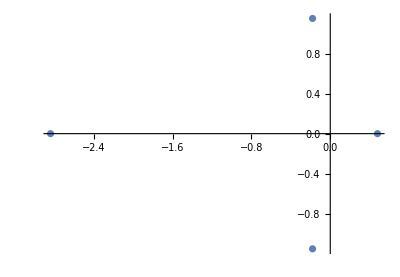

```mathematica
ComplexListPlot[ww]
```

```mathematica
(* mathematica*)
Clear[cr,cols,cr2,cr3,cr4,firstCols,s,s0]
allColors=ColorData["Legacy"][[3,1]];
firstCols={"White","AliceBlue","LightBlue" ,"Cyan","ManganeseBlue","DodgerBlue" ,"Blue","Magenta","Purple","Pink","Tomato","Red","DarkOrange","Orange","DeepNaplesYellow","Gold","Banana","Yellow","LightYellow","Orange","Pink","LightPink","Yellow","LightYellow","LightPink","White","DeepNaplesYellow", "Orange","DarkOrange","Tomato","Red","Tomato","Pink","LightPink","DeepNaplesYellow", "Orange","DarkOrange","Tomato","White","Pink","Banana","LightBlue","DodgerBlue","Cyan","White","Purple","DarkOrchid","Magenta","ManganeseBlue","DeepNaplesYellow", "Orange","DarkOrange","Tomato","GoldOchre","LightPink","Magenta","Green","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","Yellow","Tomato","DeepNaplesYellow","DodgerBlue","Cyan","Red","Blue","DeepNaplesYellow","Green","Magenta","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","LimeGreen"};
cols=ColorData["Legacy",#]&/@Join[firstCols,Complement[allColors,firstCols]];
rotate[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
cr[n_]:=cr[n]=cols[[n]];
cr2[n_]:=cr2[n]=cols[[n+4]];
cr3[n_]:=cr3[n]=cols[[n+8]];
cr4[n_]:=cr4[n]=cols[[n+12]];
cr5[n_]:=cr5[n]=cols[[n+16]]
Clear[mu,a,b,A,B]
```

```mathematica
v={-0.17957045711476127-1.1519094431252477 ⅈ,-0.17957045711476127+1.1519094431252477 ⅈ}
```

{-0.17957-1.15191 ⅈ,-0.17957+1.15191 ⅈ}

```mathematica
Abs[v]
```

{1.16582,1.16582}

```mathematica
s[1]=N[{{1+I,1},{1,1-I}}]
s[2]=N[{{1,0},{2*v[[1]],1}}]
s[3]=N[{{1,0},{2*v[[2]],1}}]
s[4]=N[{{1,0},{0,1}}]
```

{{1.+1. ⅈ,1.},{1.,1.-1. ⅈ}}

{{1.,0.},{-0.359141-2.30382 ⅈ,1.}}

{{1.,0.},{-0.359141+2.30382 ⅈ,1.}}

{{1.,0.},{0.,1.}}

```mathematica
{a,b,A,B}=Table[N[s[i]],{i,4}]
```

{{{1.+1. ⅈ,1.},{1.,1.-1. ⅈ}},{{1.,0.},{-0.359141-2.30382 ⅈ,1.}},{{1.,0.},{-0.359141+2.30382 ⅈ,1.}},{{1.,0.},{0.,1.}}}

```mathematica
Det[a]
Tr[a]
Det[b]
Tr[b]
Det[A]
Tr[A]
Det[B]
Tr[B]
```

```mathematica
Affine[{z1_,z2_}]:=0.000001 Round[(z1/z2)/0.000001];
Children[{z_,n_}]:={Affine[{a,b,A,B}[[#]].{z,1}],#}&/@Delete[Range[4],{3,4,1,2}[[n]]];
aa1={Re[#[[1]]],Im[#[[1]]]}&/@Nest[Union[Flatten[Children/@#,1]]&,ParallelTable[{Affine[{a,b,A,B}[[i]].{0,1}],i},{i,1,4}],15];
ll=Length[aa1]
Last[aa1]
aa=Delete[Reverse[Union[aa1]],1];
```

998209

{50.5976,-90.4755}

```mathematica
Length[aa]
```

751775

```mathematica
g0=ListPlot[aa,AspectRatio->Automatic,ColorFunction->"Rainbow",PlotStyle->{PointSize[0.001]},ImageSize->2000,PlotRange->{{-10,10},{-10,10}}/9];
```

```mathematica
dlst=Table[1+Mod[Floor[1+(1+Floor[12*Norm[aa[[i]]]])/(Abs[Cos[Arg[aa[[i,1]]+I*aa[[i,2]]]]]+Abs[Sin[Arg[aa[[i,1]]+I*aa[[i,2]]]]])],Length[cols]],{i,Length[aa]}];
Min[dlst]
Max[dlst]
ptlst=Point[Developer`ToPackedArray[aa],VertexColors->Developer`ToPackedArray[cr/@dlst]];
```

2

182

```mathematica
g2=Graphics[{PointSize[.001],ptlst},AspectRatio->Automatic,ImageSize->2000,PlotRange->{{-10,10},{-10,10}}/9,Background->Black];
```

```mathematica
(* end limit set*)
```

```mathematica
(*Perpendicular Hermetian inversion conformal map: z*Conjugate[z]/Abs[z]^2=1*)
```

```mathematica
bb=Delete[Reverse[Union[Table[{aa[[i,1]],-aa[[i,2]]}/(aa[[i,1]]^2+aa[[i,2]]^2),{i,Length[aa]}]]],1];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

```mathematica
g1=ListPlot[bb,AspectRatio->Automatic,ColorFunction->"Rainbow",PlotStyle->{PointSize[0.001]},ImageSize->2000,PlotRange->{{-4,4},{-4,4}}];
```

```mathematica
ptlst1a=Point[Developer`ToPackedArray[bb],VertexColors->Developer`ToPackedArray[cr/@dlst]];
```

```mathematica
g5=Rasterize[Graphics[{PointSize[.001],ptlst1a},AspectRatio->Automatic,ImageSize->2000,PlotRange->{{-4,4},{-4,4}},Background->Black],RasterSize->2000,ImageSize->2000];
```

```mathematica
(* Half plane to disk conformal map*)

bb1=Delete[Union[ParallelTable[{-(Im[-1/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,1⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,2⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]+2 Re[aa⟦i,2⟧/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]),-2 Im[aa⟦i,2⟧/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]+Re[-1/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,1⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,2⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]},{i,Length[aa]}]],Length[Union[ParallelTable[{-(Im[-1/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,1⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,2⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]+2 Re[aa⟦i,2⟧/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]),-2 Im[aa⟦i,2⟧/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]+Re[-1/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,1⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,2⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]},{i,Length[aa]}]]]];
```

```mathematica
ListPlot[bb1,PlotStyle->{{Yellow,PointSize[0.001]},{Orange,PointSize[0.001]}},ImageSize->1000,Axes->True,PlotRange->50];
```

```mathematica
ptlst3:=Point[Developer`ToPackedArray[bb1],VertexColors->Developer`ToPackedArray[cr/@dlst]];

g3=Rasterize[Graphics[{PointSize[.001],ptlst3(*,ptlst2*)},AspectRatio->Automatic,ImageSize->2000,Background->Black,PlotRange->2.5],RasterSize->2000,ImageSize->2000];
```

```mathematica
cc1=ParallelTable[{2*aa[[i,1]],2*aa[[i,2]],(1-aa[[i]].aa[[i]])}/(1+aa[[i]].aa[[i]]),{i,Length[aa]}];
```

```mathematica
ptlst5a=Point[Developer`ToPackedArray[cc1],VertexColors->Developer`ToPackedArray[cr/@dlst]];
```

```mathematica
g4=Rasterize[Graphics3D[{PointSize[.001],ptlst5a},AspectRatio->Automatic,ImageSize->2000,PlotRange->All,Background->Black,Boxed->False,ViewPoint->{2.1,2.1,2.1}],RasterSize->2000,ImageSize->2000];
```

```mathematica
Export["Nylander_3group_Entropy_Uncertainty_On_disk_scale2_limitset_15.jpg",{g0,g2,g3,g1,g4,g4}]
```

Nylander_3group_Entropy_Uncertainty_On_disk_scale2_limitset_15.jpg

```mathematica
(*end*)
```